## Notebook to calculate positron annihilation

Author: Ryan Plestid (Caltech)
For: Peiran Li (UMN)

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
|
```

```mathematica
SetMandelstam[s,t,u,p1,p2,-k1,-k2,me,me,mχ,mχ]
λ=√(s^2+me^2+me^2-2 s me^2)
SpinorUBar[p1,me].GA[μ].SpinorV[p2,me] 1/s SpinorUBar[k1,mχ].GA[μ].SpinorV[k2,mχ]
1/4% ComplexConjugate[%]//FermionSpinSum//DiracSimplify//FullSimplify
%/. u-> 2 mχ^2+2 me^2-s-t//FullSimplify
dσdt=(ϵ^2 e^4)/(64 π s)4/(s-4 me^2)%/. e-> √(4π α)//FullSimplify//Series[#,{t,0,2}]&//Normal
dσdQsq= dσdt/. t-> -Qsq//FullSimplify
```

{{}}

√(-2 me^2 s+2 me^2+s^2)

(ū(k1,mχ).(γ̄)^μ.v(k2,mχ) ū(p1,me).(γ̄)^μ.v(p2,me))/s

(2 (2 me^4+2 me^2 (2 mχ^2+s-t-u)+2 mχ^4+2 mχ^2 (s-t-u)+t^2+u^2))/s^2

(4 (t (s-2 (me^2+mχ^2))+(me^2+mχ^2)^2+t^2))/s^2+2

(4 π α^2 t ϵ^2 (s-2 (me^2+mχ^2)))/(s^3 (s-4 me^2))+(2 π α^2 ϵ^2 (2 (me^2+mχ^2)^2+s^2))/(s^3 (s-4 me^2))+(4 π α^2 t^2 ϵ^2)/(s^3 (s-4 me^2))

(2 π α^2 ϵ^2 (2 (me^2+mχ^2+Qsq)^2-2 Qsq s+s^2))/(s^3 (s-4 me^2))

```mathematica
p1cm=√(E1cm^2-me^2)/. E1cm-> √s/2;
p3cm = √(E3cm^2-mχ^2)/. E3cm-> √s/2;
(* PDG https://pdg.lbl.gov/2018/reviews/rpp2018-rev-kinematics.pdf  (47.35) *)
t0=((m1^2-m3^2-m2^2+m4^2)/(2 √s))^2 - (p1cm-p3cm)^2/. {m1-> me,m2-> me, m3-> mχ,m4-> mχ};
t1=((m1^2-m3^2-m2^2+m4^2)/(2 √s))^2 -(p1cm+p3cm)^2/. {m1-> me,m2-> me, m3-> mχ,m4-> mχ};
```

```mathematica
Integrate[dσdQsq,Qsq]
(%/. Qsq -> Qmax)- (%/. Qsq-> Qmin)/. {Qmax-> -t1,Qmin-> -t0}//FullSimplify
%/. {me->Subscript[m, e],mχ-> Subscript[m, χ]}
```

(2 π α^2 ϵ^2 (2/3 (me^2+mχ^2+Qsq)^3-Qsq^2 s+Qsq s^2))/(s^3 (s-4 me^2))

(4 π α^2 ϵ^2 (2 me^2+s) √(s-4 mχ^2) (2 mχ^2+s))/(3 s^3 √(s-4 me^2))

(4 π α^2 ϵ^2 (2 m_e^2+s) √(s-4 m_χ^2) (2 m_χ^2+s))/(3 s^3 √(s-4 m_e^2))

```mathematica
6 Subscript[m, e]^2 (√(s-4 Subscript[m, e]^2)+2 Subscript[m, χ]^2-1)+Subscript[m, χ]^2 (6 √(s-4 Subscript[m, e]^2)-2)+s (-3 √(s-4 Subscript[m, e]^2)+3 s+2)+6 Subscript[m, e]^4+6 Subscript[m, χ]^4/.√(s-4 Subscript[m, e]^2)-> √s Subscript[β, e]
%//Series[#,{Subscript[m, e],0,6}]&
```

6 m_e^2 (√s β_e+2 m_χ^2-1)+m_χ^2 (6 √s β_e-2)+6 m_e^4+s (-3 √s β_e+3 s+2)+6 m_χ^4

(m_χ^2 (6 √s β_e-2)+s (-3 √s β_e+3 s+2)+6 m_χ^4)+6 m_e^2 (√s β_e+2 m_χ^2-1)+6 m_e^4+O(m_e^7)

(8 π Qsq)/2401+(102 π)/2401

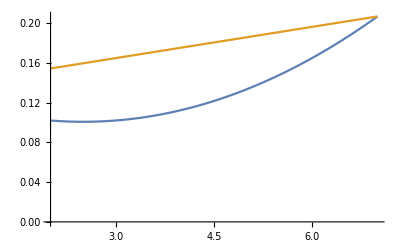

```mathematica
mχ=1;
s=4 mχ^2+3;
diff$fn=dσdQsq/. α-> 1/. ϵ-> 1/. me-> 0;
QsqMin=;
QsqMax=;
cover$fn=(((dσdQsq/. Qsq-> s)-(dσdQsq/. Qsq-> 0))/s) Qsq + (dσdQsq/. Qsq-> 0)/. α-> 1/. ϵ-> 1/. me-> 0
Plot[{diff$fn,cover$fn},{Qsq,2 mχ^2,s},{PlotRange->{0,Automatic}}]
Clear[mχ,s]
```

```mathematica
diff$fn/. Qsq-> 0
```

(102 π)/2401

```mathematica
dσdQsq/. Qsq-> 0/.α-> 1/. ϵ-> 1/. me-> 0/. s-> 4 mχ^2+3/. mχ-> 1
```

(102 π)/2401

```mathematica
Integrate[a + b t + c t^2,{t,0,tmax}]
```

a tmax+(b tmax^2)/2+(c tmax^3)/3